```mathematica
<<xlr8r.m
<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Tue 6 Jun 2017 09:55:30
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 09:55:30
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

## AddVertex-Example.nb

Example Cellzilla2D notebook.

This is virtually identical to AddCell-Example.nb

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
w=RandomizeTemplate[TemplateRectangular[{0,10,2}, {0,10,2}], .02];
```

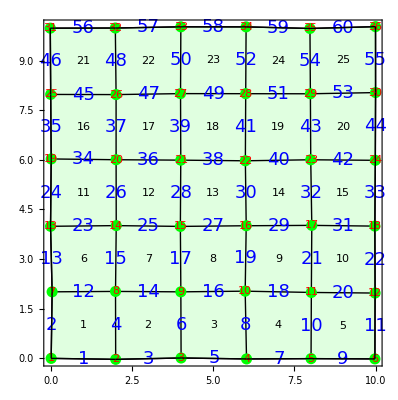

```mathematica
ShowTissue[w, Frame-> True, "Vertices"-> {Directive[Green,PointSize[.02]]},"VertexNumbers"-> {Directive[Red, FontSize-> 18]}, 
"EdgeNumbers"-> True, 
"EdgeNumberStyle"-> Directive[Blue, FontSize-> 18, FontFamily-> "Arial"],  "CellNumbers"-> True]
```

```mathematica
p=NTissueVertices[w]
```

36

```mathematica
q=NTissueEdges[w];
```

```mathematica
w1=AddVertex[w,{12.5, 0.25}];
w2=AddEdge[w1,{p+1,6}];
w3=AddEdge[w2, {p+1,12}];
w4=AddCell[w3, {q+1, q+2, 11}];
```

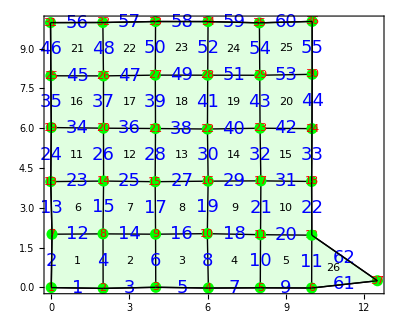

```mathematica
ShowTissue[w4, Frame-> True, "Vertices"-> {Directive[Green,PointSize[.02]]},"VertexNumbers"-> {Directive[Red, FontSize-> 18]}, 
"EdgeNumbers"-> True, 
"EdgeNumberStyle"-> Directive[Blue, FontSize-> 18, FontFamily-> "Arial"],  "CellNumbers"-> True]
```